```mathematica
Exit[]
```

```mathematica
SetOptions[NDSolve,MaxSteps->Infinity,Method->"StiffnessSwitching",AccuracyGoal->10];
SetOptions[LogLinearPlot,Frame->True];
```

## Black Holes Scalarization in Gauss Bonnet Gravity

## Reproduce analytical results from Black hole hair in generalized scalar-tensor gravity: An explicit example

## Field Equations

### Call in the Coordinate-Dep. Tensor package, define coordinates and metric

```mathematica
<<xAct`xCoba`;
<<xAct`TexAct`;
DefManifold[MC,4,IndexRange[a,n]]
DefChart[sspher,MC,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Purple]

DefScalarFunction[A]
DefScalarFunction[B]
DefScalarFunction[F]
DefConstantSymbol[α]
DefConstantSymbol[β]
DefConstantSymbol[κ]
DefConstantSymbol[η]

met=CTensor[DiagonalMatrix[{-η Exp[A[r[]]],η Exp[B[r[]]],r[]^2,r[]^2Sin[θ[]]^2}],{-sspher,-sspher}];
SetCMetric[met,sspher,SignatureOfMetric->{3,1,0}];
CD=CovDOfMetric[met];
MetricCompute[met,sspher,All,Parallelize->True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MC.

** DefVBundle: Defining vbundle TangentMC.

** DefChart: Defining chart sspher.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sspher.

** DefMapping: Defining inverse mapping isspher.

** DefTensor: Defining mapping differential tensor disspher[-a,issphera].

** DefTensor: Defining mapping differential tensor dsspher[-a,ssphera].

** DefBasis: Defining basis sspher. Coordinated basis.

** DefCovD: Defining parallel derivative PDsspher[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsspher[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsspher[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsspher[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsspher[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsspher[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsspher[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefScalarFunction: Defining scalar function F.

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol κ.

** DefConstantSymbol: Defining constant symbol η.

### Define all the tensors

WARNING: Define tensors without “:=”, it does not work properly otherwise!!!

```mathematica
G[a_,b_]=Einstein[CD][a,b];
𝒢 = ((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
meffSqrd = β/2 RicciScalar[CD][]-α((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
TPhi[a_,b_]=
1/1(CD[a]@F[r[]]CD[b]@F[r[]]-1/2 met[a,b]CD[-c]@F[r[]]CD[c]@F[r[]]	
)//ContractBasis;
TBeta[a_,b_] =1/1 (1/2 β(G[a,b](F[r[]])^2-CD[a]@CD[b]@((F[r[]])^1)+met[a,b]CD[-c]@CD[c]@((F[r[]])^1)))//ContractBasis;
TAlphaEps[a_,b_] =(*-1/1α (
2Symmetrize[met[a,-c]met[-d,b],{c,d}]epsilon[met][e,c,f,g]epsilon[met][d,h,i,l]Riemann[CD][-i,-l,-f,-g]CD[-h]@CD[-e]@(F[r[]])^1
)//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];*)
				-α(met[-c,a]met[-d,b]+met[-c,b]met[-d,a])CD[-e]@(
				CD[-f]@F[r[]]epsilon[met][f,d,h,i]epsilon[met][c,e,l,n]Riemann[CD][-l,-n,-h,-i])//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];
```

### Field Equations

```mathematica
PhiEq =CD[-a]@CD[a]@F[r[]]-meffSqrd ;
ttEq=(G[{0,sspher},{0,-sspher}]-  κ SETensor[{0,sspher},{0,-sspher}]);
rrEq=(G[{1,sspher},{1,-sspher}]-  κ SETensor[{1,sspher},{1,-sspher}]);
θθEq=(G[{2,sspher},{2,-sspher}]-  κ SETensor[{2,sspher},{2,-sspher}]);
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ]
FinalϕϕEq = PhiEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalttEq = ttEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalrrEq = rrEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalθθEq = θθEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
GaussBonnet = 𝒢//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};

FieldEqs = {FinalttEq,FinalrrEq,FinalθθEq,FinalϕϕEq}/.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r],κ->1,β->0,η^2->1,η^-2-> 1,η^-1->η};
MatrixForm[FieldEqs]
```

(-1/r^2+(ⅇ^(-B[r]) η)/r^2-(ⅇ^(-B[r]) η B'[r])/r+(12 ⅇ^(-2 B[r]) α B'[r] ϕ'[r])/r^2-(4 ⅇ^(-B[r]) α η B'[r] ϕ'[r])/r^2+1/2 ⅇ^(-B[r]) η ϕ'[r]^2-(8 ⅇ^(-2 B[r]) α ϕ''[r])/r^2+(8 ⅇ^(-B[r]) α η ϕ''[r])/r^2
-1/r^2+(ⅇ^(-B[r]) η)/r^2+(ⅇ^(-B[r]) η A'[r])/r-(12 ⅇ^(-2 B[r]) α A'[r] ϕ'[r])/r^2+(4 ⅇ^(-B[r]) α η A'[r] ϕ'[r])/r^2-1/2 ⅇ^(-B[r]) η ϕ'[r]^2
(ⅇ^(-B[r]) η A'[r])/(2 r)+1/4 ⅇ^(-B[r]) η A'[r]^2-(ⅇ^(-B[r]) η B'[r])/(2 r)-1/4 ⅇ^(-B[r]) η A'[r] B'[r]-(2 ⅇ^(-2 B[r]) α A'[r]^2 ϕ'[r])/r+(6 ⅇ^(-2 B[r]) α A'[r] B'[r] ϕ'[r])/r+1/2 ⅇ^(-B[r]) η ϕ'[r]^2+1/2 ⅇ^(-B[r]) η A''[r]-(4 ⅇ^(-2 B[r]) α ϕ'[r] A''[r])/r-(4 ⅇ^(-2 B[r]) α A'[r] ϕ''[r])/r
(2 ⅇ^(-2 B[r]) α A'[r]^2)/r^2-(2 ⅇ^(-B[r]) α η A'[r]^2)/r^2-(6 ⅇ^(-2 B[r]) α A'[r] B'[r])/r^2+(2 ⅇ^(-B[r]) α η A'[r] B'[r])/r^2+(2 ⅇ^(-B[r]) η ϕ'[r])/r+1/2 ⅇ^(-B[r]) η A'[r] ϕ'[r]-1/2 ⅇ^(-B[r]) η B'[r] ϕ'[r]+(4 ⅇ^(-2 B[r]) α A''[r])/r^2-(4 ⅇ^(-B[r]) α η A''[r])/r^2+ⅇ^(-B[r]) η ϕ''[r])

```mathematica
FieldEqs = ({{-1/r^2+(ⅇ^(-B[r]) η)/r^2-(ⅇ^(-B[r]) η B'[r])/r+(12 ⅇ^(-2 B[r]) α B'[r] ϕ'[r])/r^2-(4 ⅇ^(-B[r]) α η B'[r] ϕ'[r])/r^2+1/2 ⅇ^(-B[r]) η ϕ'[r]^2-(8 ⅇ^(-2 B[r]) α ϕ''[r])/r^2+(8 ⅇ^(-B[r]) α η ϕ''[r])/r^2}, {-1/r^2+(ⅇ^(-B[r]) η)/r^2+(ⅇ^(-B[r]) η A'[r])/r-(12 ⅇ^(-2 B[r]) α A'[r] ϕ'[r])/r^2+(4 ⅇ^(-B[r]) α η A'[r] ϕ'[r])/r^2-1/2 ⅇ^(-B[r]) η ϕ'[r]^2}, {(ⅇ^(-B[r]) η A'[r])/(2 r)+1/4 ⅇ^(-B[r]) η A'[r]^2-(ⅇ^(-B[r]) η B'[r])/(2 r)-1/4 ⅇ^(-B[r]) η A'[r] B'[r]-(2 ⅇ^(-2 B[r]) α A'[r]^2 ϕ'[r])/r+(6 ⅇ^(-2 B[r]) α A'[r] B'[r] ϕ'[r])/r+1/2 ⅇ^(-B[r]) η ϕ'[r]^2+1/2 ⅇ^(-B[r]) η A''[r]-(4 ⅇ^(-2 B[r]) α ϕ'[r] A''[r])/r-(4 ⅇ^(-2 B[r]) α A'[r] ϕ''[r])/r}, {(2 ⅇ^(-2 B[r]) α A'[r]^2)/r^2-(2 ⅇ^(-B[r]) α η A'[r]^2)/r^2-(6 ⅇ^(-2 B[r]) α A'[r] B'[r])/r^2+(2 ⅇ^(-B[r]) α η A'[r] B'[r])/r^2+(2 ⅇ^(-B[r]) η ϕ'[r])/r+1/2 ⅇ^(-B[r]) η A'[r] ϕ'[r]-1/2 ⅇ^(-B[r]) η B'[r] ϕ'[r]+(4 ⅇ^(-2 B[r]) α A''[r])/r^2-(4 ⅇ^(-B[r]) α η A''[r])/r^2+ⅇ^(-B[r]) η ϕ''[r]}});
```

These are transformation law to pass from a coordinate defined as

ⅆ s^2=-ⅇ^A[r]ⅆ t^2+ⅇ^B[r]ⅆ r^2+r^2 ⅆ Ω^2 → ⅆ s^2=-x[r]ⅆ t^2+(ⅆ r^2)/y[r]+r^2 ⅆ Ω^2.

```mathematica
Trasf = {ⅇ^A[r]->x[r],ⅇ^(-B[r])->y[r],ⅇ^(A[r]-2 B[r])->x[r] y[r]^2,ⅇ^(A[r]- B[r])->x[r]y[r],ⅇ^B[r]->y[r]^-1,ⅇ^(2 B[r])->y[r]^-2,B'[r]->-D[Log[y[r]],r],ⅇ^(-B[r])->y[r],A'[r]->D[Log[x[r]],r],ⅇ^B[r]->y[r]^-1,ⅇ^(-2 B[r])->y[r]^2,ⅇ^B[r]->y[r]^-1,A'[r]^2->D[Log[x[r]],r]^2,A'[r]->D[Log[x[r]],r],B'[r]->-D[Log[y[r]],r],A''[r]->D[Log[x[r]],{r,2}]};
```

```mathematica
𝒢/.{r[]->r}/.Trasf//Simplify
```

(-2 η x[r] x'[r] y'[r]-2 y[r]^2 (x'[r]^2-2 x[r] x''[r])+2 y[r] (η x'[r]^2+3 x[r] x'[r] y'[r]-2 η x[r] x''[r]))/(r^2 η^2 x[r]^2)

```mathematica
GB[r_]:=(-2 η x[r] x'[r] y'[r]-2 y[r]^2 (x'[r]^2-2 x[r] x''[r])+2 y[r] (η x'[r]^2+3 x[r] x'[r] y'[r]-2 η x[r] x''[r]))/(r^2 η^2 x[r]^2);
```

### Define the System of Equations

Solve algebraically the rr-equation (get eqs. 24-25)

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,β,η]
rrSolveEq=FieldEqs[[2]]/.{Exp[B[r]]->x[r],Exp[-B[r]]->(x[r])^-1,Exp[2B[r]]->(x[r])^2,Exp[-2B[r]]->(x[r])^-2,Exp[3B[r]]->(x[r])^3,Exp[6B[r]]->(x[r])^6,Exp[-3B[r]]->(x[r])^-3,Exp[-6B[r]]->(x[r])^-6,η^2->1};
Solve[rrSolveEq==0,x[r]][[2]]//FullSimplify
```

{x[r]→1/4 (2 η+2 r η A'[r]+8 α η A'[r] ϕ'[r]-r^2 η ϕ'[r]^2+√(-192 α A'[r] ϕ'[r]+η^2 (2-r^2 ϕ'[r]^2+2 A'[r] (r+4 α ϕ'[r]))^2))}

```mathematica
Γ = -η(1+1 r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2);
rrSolution[r_] := (-Γ+√(Γ^2-48α A'[r] ϕ'[r]))/2;
```

```mathematica
rrSolution[r]^-1
```

2/(η (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)+√(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2))

```mathematica
D[rrSolution[r]^-1,r]
```

-((2 (η (A'[r]-r ϕ'[r]^2+r A''[r]+4 α ϕ'[r] A''[r]+4 α A'[r] ϕ''[r]-r^2 ϕ'[r] ϕ''[r])+(-48 α ϕ'[r] A''[r]-48 α A'[r] ϕ''[r]+2 η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2) (A'[r]-r ϕ'[r]^2+r A''[r]+4 α ϕ'[r] A''[r]+4 α A'[r] ϕ''[r]-r^2 ϕ'[r] ϕ''[r]))/(2 √(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2))))/(η (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)+√(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2))^2)

```mathematica
ySolution[r_]:=2/(η (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)+√(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2));
yPrimeSolution[r_]:=-((2 (η (A'[r]-r ϕ'[r]^2+r A''[r]+4 α ϕ'[r] A''[r]+4 α A'[r] ϕ''[r]-r^2 ϕ'[r] ϕ''[r])+(-48 α ϕ'[r] A''[r]-48 α A'[r] ϕ''[r]+2 η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2) (A'[r]-r ϕ'[r]^2+r A''[r]+4 α ϕ'[r] A''[r]+4 α A'[r] ϕ''[r]-r^2 ϕ'[r] ϕ''[r]))/(2 √(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2))))/(η (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)+√(-48 α A'[r] ϕ'[r]+η^2 (1+r A'[r]+4 α A'[r] ϕ'[r]-1/2 r^2 ϕ'[r]^2)^2))^2)
```

Then, take the derivative of rr-equation and solve for B’[r], then from θθ-equation get A’’[r] and from the scalar equation get ϕ’’[r].

```mathematica
BPrime = Solve[D[FieldEqs[[2]],r]==0,B'[r]][[1]]//FullSimplify;
APPrime = Solve[(FieldEqs[[3]]/.BPrime)==0, A''[r]][[1]]//FullSimplify;
PhiPPrime = Solve[((FieldEqs[[4]]/.BPrime/.APPrime)//Simplify)==0, ϕ''[r]][[1]]//Simplify;
```

Gathering everything together one has that the field equations (eqs 26-27):

```mathematica
PhiEquation = PhiPPrime/.Rule->Subtract;
AEquation = (APPrime/.PhiPPrime//Simplify)/.Rule->Subtract;
ODEqs = {PhiEquation[[1]],AEquation[[1]]}/.{η^2->1};
```

```mathematica
ODEqs={(ⅇ^B[r] η (8 r α A'[r]^3 (r-8 α ϕ'[r]) (ⅇ^B[r] r η+4 α (-3+ⅇ^B[r] η) ϕ'[r])-2 ⅇ^B[r] (8 α (-1+ⅇ^B[r] η)+ⅇ^B[r] r^3 η ϕ'[r]-8 r^2 α ϕ'[r]^2) (2 ⅇ^B[r]-2 η+r^2 η ϕ'[r]^2)+2 A'[r]^2 (8 ⅇ^B[r] r^2 α η (1+ⅇ^B[r] η)+r (ⅇ^(2 B[r]) r^4+32 α^2 (-3+ⅇ^(2 B[r])-6 ⅇ^B[r] η)) ϕ'[r]-4 α (-ⅇ^B[r] r^4 η (-6+ⅇ^B[r] η)+128 α^2 (-3+ⅇ^B[r] η)) ϕ'[r]^2+96 r^3 α^2 ϕ'[r]^3)+A'[r] (8 (ⅇ^(2 B[r]) r^4+16 α^2 (3+3 ⅇ^(2 B[r])-6 ⅇ^B[r] η)) ϕ'[r]+16 ⅇ^B[r] r^3 α η (-11+2 ⅇ^B[r] η) ϕ'[r]^2-r^2 (ⅇ^(2 B[r]) r^4-32 α^2 (27+ⅇ^(2 B[r])-8 ⅇ^B[r] η)) ϕ'[r]^3+8 ⅇ^B[r] r^5 α η ϕ'[r]^4)))/(2 r A'[r] (64 α^2 (-1+ⅇ^B[r] η) A'[r] (-ⅇ^B[r] r η+2 α (3+ⅇ^B[r] η) ϕ'[r])-ⅇ^B[r] η (-ⅇ^(2 B[r]) r^4+32 α^2 (-1+ⅇ^B[r] η)^2+16 ⅇ^B[r] r^3 α η ϕ'[r]-64 r^2 α^2 ϕ'[r]^2)))+ϕ''[r],-((32 r α^2 A'[r]^4 (ⅇ^B[r] r η (-5+3 ⅇ^B[r] η)-16 α (-3+2 ⅇ^B[r] η) ϕ'[r])+4 ⅇ^(3 B[r]) r^2 (2 ⅇ^B[r]-2 η+r^2 η ϕ'[r]^2)-2 A'[r]^3 (ⅇ^(3 B[r]) r^5 η^3-32 ⅇ^B[r] r α^2 η (-7+3 ⅇ^B[r] η)-4 α (-ⅇ^(2 B[r]) r^4 (-5+ⅇ^B[r] η)+64 α^2 (-3+ⅇ^B[r] η)^2) ϕ'[r]-16 ⅇ^B[r] r^3 α^2 η (-5+3 ⅇ^B[r] η) ϕ'[r]^2)-ⅇ^B[r] A'[r]^2 (8 (-64 ⅇ^B[r] α^2+48 α^2 η+ⅇ^(2 B[r]) (r^4+16 α^2) η)+48 ⅇ^B[r] r^3 α (-3+ⅇ^B[r] η) ϕ'[r]-r^2 η (ⅇ^(2 B[r]) r^4-32 α^2 (21+ⅇ^(2 B[r])-18 ⅇ^B[r] η)) ϕ'[r]^2+16 ⅇ^B[r] r^5 α ϕ'[r]^3)+2 ⅇ^(2 B[r]) r^2 η A'[r] (2 ⅇ^B[r] r (ⅇ^B[r]-3 η) η-32 α (2 ⅇ^B[r]-3 η) ϕ'[r]+ⅇ^B[r] r^3 ϕ'[r]^2-8 r^2 α η ϕ'[r]^3))/(2 r A'[r] (64 α^2 (-1+ⅇ^B[r] η) A'[r] (-ⅇ^B[r] r η+2 α (3+ⅇ^B[r] η) ϕ'[r])-ⅇ^B[r] η (-ⅇ^(2 B[r]) r^4+32 α^2 (-1+ⅇ^B[r] η)^2+16 ⅇ^B[r] r^3 α η ϕ'[r]-64 r^2 α^2 ϕ'[r]^2))))+A''[r]};
```

### Analytic Conditions @ Horizon

Let’s expand the e^B expression near the horizon

```mathematica
Series[rrSolution[r]/.{η->1},{A'[r],∞,0}]//FullSimplify
Series[rrSolution[r]/.{η->-1},{A'[r],-∞,0}]//FullSimplify
```

((r A'[r]+4 α A'[r] ϕ'[r]+√(A'[r]^2 (r+4 α ϕ'[r])^2)) A'[r])/(2 A'[r])+(2 r A'[r]-40 α A'[r] ϕ'[r]-r^3 A'[r] ϕ'[r]^2-4 r^2 α A'[r] ϕ'[r]^3+2 √(A'[r]^2 (r+4 α ϕ'[r])^2)-r^2 ϕ'[r]^2 √(A'[r]^2 (r+4 α ϕ'[r])^2))/(4 √(A'[r]^2 (r+4 α ϕ'[r])^2))+O[1/A'[r]]^1

((-r A'[r]-4 α A'[r] ϕ'[r]+√(A'[r]^2 (r+4 α ϕ'[r])^2)) A'[r])/(2 A'[r])+(2 r A'[r]-40 α A'[r] ϕ'[r]-r^3 A'[r] ϕ'[r]^2-4 r^2 α A'[r] ϕ'[r]^3-2 √(A'[r]^2 (r+4 α ϕ'[r])^2)+r^2 ϕ'[r]^2 √(A'[r]^2 (r+4 α ϕ'[r])^2))/(4 √(A'[r]^2 (r+4 α ϕ'[r])^2))+O[1/A'[r]]^1

```mathematica
((r A'[r]+4 α A'[r] ϕ'[r]+A'[r] (r+4 α ϕ'[r])) A'[r])/(2 A'[r])+1/(4 A'[r] (r+4 α ϕ'[r]))(2 r A'[r]-40 α A'[r] ϕ'[r]-r^3 A'[r] ϕ'[r]^2-4 r^2 α A'[r] ϕ'[r]^3+2 A'[r] (r+4 α ϕ'[r])-r^2 ϕ'[r]^2 A'[r] (r+4 α ϕ'[r]))//FullSimplify (*Second Term *)
```

-2-1/2 r^2 ϕ'[r]^2+(3 r)/(r+4 α ϕ'[r])+A'[r] (r+4 α ϕ'[r])

The leading term can be expressed as

```mathematica
LeadTerm =η( A'[r] (r+4 α ϕ'[r])-((r^2 ϕ'[r]^2)/2+(8 α ϕ'[r]-r)/(4 α ϕ'[r]+r))) (* Consistent. From inside A->-∞, is negative so the √(A^('2))should be written as -A'*)
```

η (-1/2 r^2 ϕ'[r]^2+A'[r] (r+4 α ϕ'[r])-(-r+8 α ϕ'[r])/(r+4 α ϕ'[r]))

```mathematica
NewSys = ODEqs/.{Exp[B[r]]->x[r],Exp[-B[r]]->(x[r])^-1,Exp[2B[r]]->(x[r])^2,Exp[-2B[r]]->(x[r])^-2};

HorExpansion = NewSys/.{x[r]->LeadTerm};
Series[HorExpansion,A'[r]->∞]/.{κ->1,η^2->1}//Simplify
```

{((r+4 α ϕ'[r]) (12 α+r^3 ϕ'[r]+4 r^2 α ϕ'[r]^2) A'[r])/(r^4-96 α^2+4 r^3 α ϕ'[r])+O[1/A'[r]]^0,(4 α (-12 α+r^3 ϕ'[r]+4 r^2 α ϕ'[r]^2) A'[r]^2)/(r^4-96 α^2+4 r^3 α ϕ'[r])+1/O[1/A'[r]]}

```mathematica
Solve[ (12 α+r^3 ϕ'[r]+4 r^2 α ϕ'[r]^2)==0,ϕ'[r]]//FullSimplify
```

{{ϕ'[r]→-(r^3+√(r^6-192 r^2 α^2))/(8 r^2 α)},{ϕ'[r]→(-r^3+√(r^6-192 r^2 α^2))/(8 r^2 α)}}

```mathematica
PhiPrimeHorizon = (-r+√(r^4-192 α^2))/(8 r α);
```

## Boundary Conditions

### Perturbative Solution @ Horizon

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
ODEsysytem = FieldEqs/.Trasf//Expand;

HorizonSystem = Solve[ODEsysytem==0,{ϕ''[r],x'[r],y'[r],x''[r]}][[1]][[1;;3]]/.{Rule->Subtract};
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=∑_(i=1)^4 Subscript[a, i](r-1)^i; (*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=∑_(i=1)^5 Subscript[b, i](r-1)^i;(* these definitions will be inserted in the system*)
ϕ[r_]:=∑_(i=0)^5 Subscript[f, i](r-1)^i;
```

```mathematica
HorEqs = Series[{HorizonSystem[[1]](r-1),HorizonSystem[[2]],HorizonSystem[[3]]},{r,1,4}];
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,3}];
HorEqs2 = Table[SeriesCoefficient[HorEqs[[i]],1],{i,1,3}];
```

```mathematica
HorFirst = Solve[HorEqs1==0,{Subscript[f, 1],Subscript[b, 1]}][[2]]/.{η^2->1,η^4->1,η^-2->1,η^-1->η} (* Consistent with previous result (ϕ'[Subscript[r, h]]=Subscript[f, 1]) *)
HorSecond =Solve[HorEqs2==0,{Subscript[f, 2],Subscript[b, 2],Subscript[a, 2]}][[1]];
```

{f_1→(-1+√(1-192 α^2))/(8 α),b_1→((1/α-(√(1-192 α^2))/α) η)/(96 α)}

```mathematica
HorSolution = {∑_(i=1)^2 Subscript[a, i](r-1)^i,∑_(i=1)^2 Subscript[b, i](r-1)^i,∑_(i=0)^2 Subscript[f, i](r-1)^i,D[∑_(i=0)^2 Subscript[f, i](r-1)^i,r]}/.HorSecond/.HorFirst;
```

### Perturbative Solution @ Infinity

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
ODEsysytem = FieldEqs/.Trasf//Expand;

InfSystem = Solve[ODEsysytem==0,{ϕ''[r],x'[r],y'[r],x''[r]}][[1]][[1;;3]]/.{Rule->Subtract}/.{η->1};
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=1+∑_(i=1)^4 Subscript[a, i](r)^-i ;(*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=1+∑_(i=1)^4 Subscript[b, i](r)^-i;(* these definitions will be inserted in the system*)
ϕ[r_]:=∑_(i=0)^4 Subscript[f, i](r)^-i;
```

```mathematica
InfEqs = Series[{InfSystem[[1]] r^4,InfSystem[[2]] r^2,InfSystem[[3]] r^3},{r,∞,5}];
InfEqs1 = Table[SeriesCoefficient[InfEqs[[i]],0],{i,1,3}];
InfEqs2 = Table[SeriesCoefficient[InfEqs[[i]],1],{i,1,3}];
InfEqs3 = Table[SeriesCoefficient[InfEqs[[i]],2],{i,1,3}];
InfEqs4 = Table[SeriesCoefficient[InfEqs[[i]],4],{i,1,3}];

InfFirst = Solve[InfEqs1==0,{Subscript[f, 2],Subscript[a, 1],Subscript[b, 2]}][[1]];
InfSecond = Solve[InfEqs2==0,{Subscript[f, 3],Subscript[a, 2],Subscript[b, 3]}][[1]]/.InfFirst//FullSimplify;
InfThird = Solve[InfEqs3==0,{Subscript[f, 4],Subscript[a, 3],Subscript[b, 4]}][[1]]/.InfSecond/.InfFirst//FullSimplify;
InfFourth = Solve[InfEqs4[[2]]==0,{Subscript[a, 4]}][[1]]/.InfThird/.InfSecond/.InfFirst//FullSimplify;
```

```mathematica
;
```

```mathematica
InfCondition = Join[InfFirst,InfSecond,InfThird,InfFourth]/.{η->1};
InfSolution=Collect[{x[r],y[r],ϕ[r]}//.InfCondition/.Subscript[b, 1]->-2M/.Subscript[f, 1]->Q/.Subscript[f, 0]->0,r,Simplify]
```

{1+(M Q^2)/(6 r^3)-(2 M)/r-(Q (-16 M^2 Q+Q^3-192 M α))/(12 r^4),1+(M Q^2)/(2 r^3)+Q^2/(2 r^2)-(2 M)/r+(2 M Q (M Q+24 α))/(3 r^4),-(Q (-16 M^2+Q^2))/(12 r^3)+(M Q)/r^2+Q/r+(2 M^3 Q-(M Q^3)/3-4 M^2 α)/r^4}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
```

```mathematica
Solve[{1+(Ms Qs^2)/(2 r^3)+Qs^2/(2 r^2)-(2 Ms)/r,-Qs/r^2}=={y[r],ϕ'[r]},{Qs,Ms}]//Simplify
```

{{Qs→-r^2 ϕ'[r],Ms→-(r (2-2 y[r]+r^2 ϕ'[r]^2))/(-4+r^2 ϕ'[r]^2)}}

```mathematica
192^(1/4)
```

2 √2 3^(1/4)

```mathematica
16*12
```

192

## Numerical Integration

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
SYS = ODEqs/.{Exp[B[r]]->rrSolution[r],Exp[2B[r]]->(rrSolution[r])^2,Exp[3B[r]]->(rrSolution[r])^3}/.Trasf;
```

```mathematica
IntOut[αc_,ϕh_?NumericQ,δ_,rMax_]:=(
rInit = 1+δ;
BoundA = HorSolution[[1]]/.{α->αc,η->1};
PhiPrimeHorizon=HorSolution[[4]]/.{α->αc,η->1};
BOUND =
{
ϕ[rInit] ==  ϕh,
ϕ'[rInit] ==  PhiPrimeHorizon/.{r->rInit},
x[rInit] == BoundA/.{r->rInit},
x'[rInit] == D[BoundA,r]/.{r->rInit}
}/.{α->αc,Subscript[a, 1]->1,η->1};
EQS = {SYS =={0,0}}/.{α->αc,η->1};
SOLOUT = NDSolve[Join[BOUND,EQS],{x,ϕ},{r,rInit,rMax}][[1]];
grr[r]=rrSolution[r]/.SOLOUT;
ϕ[100]/.SOLOUT
)

IntIn[αc_,ϕh_?NumericQ,δ_,rMin_]:=(
rInit = 1-δ;
BoundA = HorSolution[[1]]/.{α->αc,η->-1};
PhiPrimeHorizon=HorSolution[[4]]/.{α->αc,η->1};
BOUND =
{
ϕ[rInit] ==  ϕh,
ϕ'[rInit] ==  PhiPrimeHorizon/.{r->rInit},
x[rInit] == BoundA/.{r->rInit},
x'[rInit] == D[BoundA,r]/.{r->rInit}
}/.{α->αc,Subscript[a, 1]->1,η->-1};
EQS = {SYS =={0,0}}/.{α->αc,η->-1};
SOLIN = NDSolve[Join[BOUND,EQS],{x,ϕ},{r,rInit,rMin}][[1]];
)

ShootingPhi[α_,δ_,rMax_]:=(InfPhi[f_?NumericQ]:=IntOut[α,f,δ,rMax];
f/.FindRoot[InfPhi[f],{f,0.2}]
)
```

```mathematica
ScalarProfile[αc_,rMax_,rMin_,δ_]:=(
phiH = ShootingPhi[αc,δ,rMax];
IntIn[αc,phiH,δ,rMin];
GAUSBONNET[r_]:={GB[r]/.{y[r]->ySolution[r],y'[r]->yPrimeSolution[r]}}/.Trasf;

SetDirectory[NotebookDirectory[]];

Points1 = Table[{r,ϕ[r]/.SOLOUT},{r,1+δ,5,0.01}];
Points2 = Table[{r,Re[ϕ[r]]/.SOLIN},{r,rMin,1-δ,0.01}];
Export["GB_Field.txt",Join[Points2,Points1],"Table"];

Points1 = Table[{r,Log[x[r]]/.SOLOUT},{r,1+δ,5,0.01}];
Points2 = Table[{r,Re[Log[x[r]]]/.SOLIN},{r,rMin,1-δ,0.01}];
Export["GB_A.txt",Join[Points2,Points1],"Table"];

Points1 = Table[{r,Log[Re[rrSolution[r]]]/.Trasf/.SOLOUT/.{η->1,α->αc}},{r,1+δ,5,0.01}];
Points2 = Table[{r,Log[Re[rrSolution[r]]]/.Trasf/.SOLIN/.{η->-1,α->αc}},{r,rMin,1-δ,0.01}];
Export["GB_B.txt",Join[Points2,Points1],"Table"];

Points1 = Table[{r,Log[Re[GAUSBONNET[r]]]/.SOLOUT/.{η->+1,α->αc}},{r,1+δ,5,0.01}];
Points2 = Table[{r,Log[Re[GAUSBONNET[r]]]/.SOLIN/.{η->-1,α->αc}},{r,rMin,1-δ,0.01}];
Export["GB_GB.txt",Join[Points2,Points1],"Table"];

Points2 = Table[{r,((Re[GAUSBONNET[r]][[1]]/.SOLIN/.{η->-1,α->αc})-12 r^-6)/(12 r^-6)},{r,rMin,0.35,0.001}];
Export["GB_DIFF.txt",Points2,"Table"];

{Show[
Plot[{Re[ϕ[r]]/.SOLOUT},{r,1+δ,5},PlotRange->{{0,5},{0,0.25}},Frame->True],
Plot[Re[ϕ[r]]/.SOLIN,{r,rMin,1-δ}]],
Show[
Plot[{Log[x[r]]/.SOLOUT},{r,1+δ,5},PlotRange->{{0,5},{-6,1}},Frame->True],
Plot[Re[Log[x[r]]]/.SOLIN,{r,rMin,1-δ},PlotRange->{{0,5},{-6,1}},Frame->True]
],
Show[
Plot[{Log[Re[rrSolution[r]]]/.Trasf/.SOLOUT/.{η->1,α->αc}},{r,1+δ,5},PlotRange->{{0,5},{-1,6}},Frame->True],
Plot[Log[Re[rrSolution[r]]]/.Trasf/.SOLIN/.{η->-1,α->αc},{r,rMin,1-δ},PlotRange->{{0,5},{-1,6}},Frame->True]
],
Show[
Plot[Log[Re[GAUSBONNET[r]]]/.SOLOUT/.{η->+1,α->αc},{r,1+δ,5},PlotRange->All,Frame->True],
Plot[Log[Re[GAUSBONNET[r]]]/.SOLIN/.{η->-1,α->αc},{r,rMin,1-δ},PlotRange->All,Frame->True]
],
Show[
Plot[{((Re[GAUSBONNET[r]]/.SOLIN/.{η->-1,α->αc})-12 r^-6)/(12 r^-6)},{r,rMin,0.5},PlotRange->All,Frame->True]]
}
)
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
```

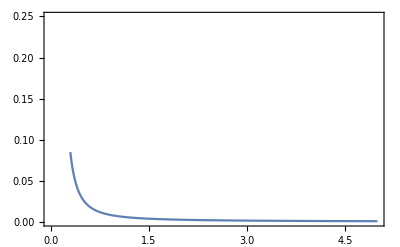
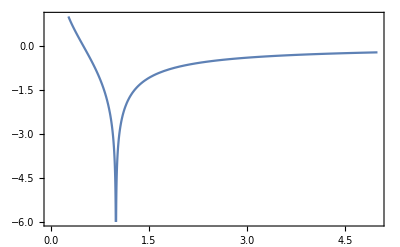
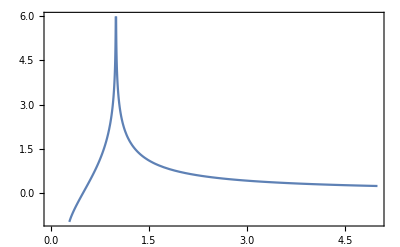
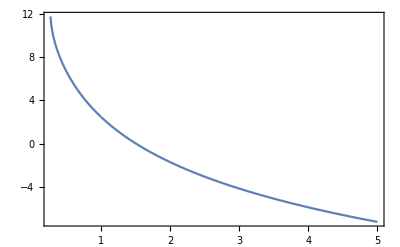
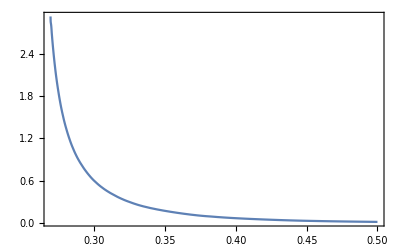

```mathematica
ScalarProfile[0.001,200,0.269,10^-4]
```

```mathematica
Table[{r,((Re[GAUSBONNET[r]][[1]]/.SOLIN/.{η->-1,α->0.001})-12 r^-6)/(12 r^-6)},{r,0.296,0.5,0.005}]
```

{{0.296,0.683403},{0.301,0.577241},{0.306,0.494518},{0.311,0.428754},{0.316,0.374029},{0.321,0.327881},{0.326,0.28995},{0.331,0.256433},{0.336,0.229255},{0.341,0.206396},{0.346,0.186519},{0.351,0.168767},{0.356,0.152639},{0.361,0.137897},{0.366,0.12451},{0.371,0.112608},{0.376,0.10245},{0.381,0.0944025},{0.386,0.0866349},{0.391,0.0794233},{0.396,0.0731175},{0.401,0.0675141},{0.406,0.0624556},{0.411,0.0578238},{0.416,0.0535341},{0.421,0.0495312},{0.426,0.0457847},{0.431,0.0422862},{0.436,0.0390459},{0.441,0.0360902},{0.446,0.0334593},{0.451,0.0312047},{0.456,0.0293165},{0.461,0.0272765},{0.466,0.0254507},{0.471,0.0237973},{0.476,0.0222826},{0.481,0.0208803},{0.486,0.0195704},{0.491,0.0183387},{0.496,0.0171765}}